```mathematica
SetDirectory[NotebookDirectory[]]
```

SetDirectory[$Failed]

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

SetDirectory::badfile: The specified argument, $Failed, should be a valid string or File object.

```mathematica
Get["library/FeynCalc.m"]
```

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_], LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

## Explicit Gell-Mann matrices

```mathematica
Λ={{{0,0,0},{0,0,1/(2 √3)},{0,1/(2 √3),0}},{{0,0,1/(2 √3)},{0,0,0},{1/(2 √3),0,0}},{{0,1/(2 √3),0},{1/(2 √3),0,0},{0,0,0}},{{1/(2 √3),0,0},{0,-1/(2 √3),0},{0,0,0}},{{-1/6,0,0},{0,-1/6,0},{0,0,1/3}}};
```

```mathematica
dband[k_]:=3{k.Λ[[1]].k,k.Λ[[2]].k,k.Λ[[3]].k,k.Λ[[4]].k,k.Λ[[5]].k}
```

## Spin 3/2 matrices

```mathematica
Sz=1/2{{3,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-3}};
Sx=1/2{{0,√3,0,0},{√3,0,2,0},{0,2,0,√3},{0,0,√3,0}};
Sy=1/2{{0,-I √3,0,0},{I √3,0,-I 2,0},{0,I 2,0,-I √3},{0,0,I √3,0}};
```

```mathematica
idM={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
Comm[X_,Y_]:=X.Y-Y.X
```

```mathematica
AntiComm[X_,Y_]:=X.Y+Y.X
```

## Gamma matrices

```mathematica
Γ={1/(√3)(Sy.Sz+Sz.Sy),1/(√3)(Sz.Sx+Sx.Sz),1/(√3)(Sx.Sy+Sy.Sx),1/(√3)(Sx.Sx-Sy.Sy),Sz.Sz-5/4 idM};
```

```mathematica
Γ[[1]]//MatrixForm
```

(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0)

```mathematica
Γ[[2]]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0)

```mathematica
Tr
```

Tr

```mathematica
A={{0,0,0,1/4,(√3)/4},{0,0,1/4,0,0},{0,-1/4,0,0,0},{-1/4,0,0,0,0},{(-√3)/4,0,0,0,0}}
```

{{0,0,0,1/4,(√3)/4},{0,0,1/4,0,0},{0,-1/4,0,0,0},{-1/4,0,0,0,0},{-(√3)/4,0,0,0,0}}

```mathematica
A+Aᵀ
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
B={{0,0,1/4,0,0},{0,0,0,1/4,(-√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}}
```

{{0,0,1/4,0,0},{0,0,0,1/4,-(√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}}

```mathematica
B+Bᵀ
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
CC={{0,-1/4,0,0,0},{1/4,0,0,0,0},{0,0,0,-1/2,0},{0,0,1/2,0,0},{0,0,0,0,0}}
```

{{0,-1/4,0,0,0},{1/4,0,0,0,0},{0,0,0,-1/2,0},{0,0,1/2,0,0},{0,0,0,0,0}}

```mathematica
CC+CCᵀ
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
η={A,B,CC}
```

{{{0,0,0,1/4,(√3)/4},{0,0,1/4,0,0},{0,-1/4,0,0,0},{-1/4,0,0,0,0},{-(√3)/4,0,0,0,0}},{{0,0,1/4,0,0},{0,0,0,1/4,-(√3)/4},{-1/4,0,0,0,0},{0,-1/4,0,0,0},{0,(√3)/4,0,0,0}},{{0,-1/4,0,0,0},{1/4,0,0,0,0},{0,0,0,-1/2,0},{0,0,1/2,0,0},{0,0,0,0,0}}}

```mathematica
Bx η[[1]]+By η[[2]]+Bz η[[3]]//MatrixForm
```

(0 | -Bz/4 | By/4 | Bx/4 | (√3 Bx)/4
Bz/4 | 0 | Bx/4 | By/4 | -(√3 By)/4
-By/4 | -Bx/4 | 0 | -Bz/2 | 0
-Bx/4 | -By/4 | Bz/2 | 0 | 0
-(√3 Bx)/4 | (√3 By)/4 | 0 | 0 | 0)

```mathematica
{Bx,By,Bz}.η//MatrixForm
```

(0 | -Bz/4 | By/4 | Bx/4 | (√3 Bx)/4
Bz/4 | 0 | Bx/4 | By/4 | -(√3 By)/4
-By/4 | -Bx/4 | 0 | -Bz/2 | 0
-Bx/4 | -By/4 | Bz/2 | 0 | 0
-(√3 Bx)/4 | (√3 By)/4 | 0 | 0 | 0)

```mathematica
SpinG[a_,b_]:=Comm[Γ[[a]],Γ[[b]]]/(2I)
```

```mathematica
SpinG[1,2].SpinG[1,2]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
SpinG[1,3].SpinG[1,3]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
SpinG[1,4].SpinG[1,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
SpinG[1,5].SpinG[1,5]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
SpinG[5,3].SpinG[5,3]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
DisP[k_,B_,g_]:=Module[{a,b,X,Y,Z,W},X=B.η;Y=Sum[SpinG[a,b]X[[a,b]],{a,1,5},{b,1,5}];Eigenvalues[Z=1/2(dband[k].Γ+g Y)]]
```

```mathematica
DisP[{px,py,pz},{Hx,Hy,Hz},g]
```

{1/32 Root[36864 g^4 Hx^4-57344 g^4 Hx^2 Hy^2+36864 g^4 Hy^4-57344 g^4 Hx^2 Hz^2+73728 g^4 Hy^2 Hz^2+36864 g^4 Hz^4-163840 g^2 Hx^2 px^4+32768 g^2 Hy^2 px^4+32768 g^2 Hz^2 px^4+65536 px^8+393216 g^2 Hx Hy px^3 py-131072 g^2 Hx^2 px^2 py^2-131072 g^2 Hy^2 px^2 py^2+65536 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-393216 g^2 Hx Hy px py^3+32768 g^2 Hx^2 py^4-163840 g^2 Hy^2 py^4+32768 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+393216 g^2 Hx Hz px^3 pz-393216 g^2 Hy Hz px^2 py pz-393216 g^2 Hx Hz px py^2 pz-393216 g^2 Hy Hz py^3 pz-131072 g^2 Hx^2 px^2 pz^2+65536 g^2 Hy^2 px^2 pz^2-131072 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-393216 g^2 Hx Hy px py pz^2+65536 g^2 Hx^2 py^2 pz^2-131072 g^2 Hy^2 py^2 pz^2-131072 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-393216 g^2 Hx Hz px pz^3-393216 g^2 Hy Hz py pz^3+32768 g^2 Hx^2 pz^4+32768 g^2 Hy^2 pz^4-163840 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(16384 g^2 Hx^2 px^2+8192 g^2 Hy^2 px^2+8192 g^2 Hz^2 px^2-49152 g^2 Hx Hy px py-8192 g^2 Hx^2 py^2-16384 g^2 Hy^2 py^2+8192 g^2 Hz^2 py^2-49152 g^2 Hx Hz px pz-49152 g^2 Hy Hz py pz-8192 g^2 Hx^2 pz^2+8192 g^2 Hy^2 pz^2-16384 g^2 Hz^2 pz^2) #1+(-640 g^2 Hx^2-640 g^2 Hy^2-640 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,1],1/32 Root[36864 g^4 Hx^4-57344 g^4 Hx^2 Hy^2+36864 g^4 Hy^4-57344 g^4 Hx^2 Hz^2+73728 g^4 Hy^2 Hz^2+36864 g^4 Hz^4-163840 g^2 Hx^2 px^4+32768 g^2 Hy^2 px^4+32768 g^2 Hz^2 px^4+65536 px^8+393216 g^2 Hx Hy px^3 py-131072 g^2 Hx^2 px^2 py^2-131072 g^2 Hy^2 px^2 py^2+65536 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-393216 g^2 Hx Hy px py^3+32768 g^2 Hx^2 py^4-163840 g^2 Hy^2 py^4+32768 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+393216 g^2 Hx Hz px^3 pz-393216 g^2 Hy Hz px^2 py pz-393216 g^2 Hx Hz px py^2 pz-393216 g^2 Hy Hz py^3 pz-131072 g^2 Hx^2 px^2 pz^2+65536 g^2 Hy^2 px^2 pz^2-131072 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-393216 g^2 Hx Hy px py pz^2+65536 g^2 Hx^2 py^2 pz^2-131072 g^2 Hy^2 py^2 pz^2-131072 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-393216 g^2 Hx Hz px pz^3-393216 g^2 Hy Hz py pz^3+32768 g^2 Hx^2 pz^4+32768 g^2 Hy^2 pz^4-163840 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(16384 g^2 Hx^2 px^2+8192 g^2 Hy^2 px^2+8192 g^2 Hz^2 px^2-49152 g^2 Hx Hy px py-8192 g^2 Hx^2 py^2-16384 g^2 Hy^2 py^2+8192 g^2 Hz^2 py^2-49152 g^2 Hx Hz px pz-49152 g^2 Hy Hz py pz-8192 g^2 Hx^2 pz^2+8192 g^2 Hy^2 pz^2-16384 g^2 Hz^2 pz^2) #1+(-640 g^2 Hx^2-640 g^2 Hy^2-640 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,2],1/32 Root[36864 g^4 Hx^4-57344 g^4 Hx^2 Hy^2+36864 g^4 Hy^4-57344 g^4 Hx^2 Hz^2+73728 g^4 Hy^2 Hz^2+36864 g^4 Hz^4-163840 g^2 Hx^2 px^4+32768 g^2 Hy^2 px^4+32768 g^2 Hz^2 px^4+65536 px^8+393216 g^2 Hx Hy px^3 py-131072 g^2 Hx^2 px^2 py^2-131072 g^2 Hy^2 px^2 py^2+65536 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-393216 g^2 Hx Hy px py^3+32768 g^2 Hx^2 py^4-163840 g^2 Hy^2 py^4+32768 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+393216 g^2 Hx Hz px^3 pz-393216 g^2 Hy Hz px^2 py pz-393216 g^2 Hx Hz px py^2 pz-393216 g^2 Hy Hz py^3 pz-131072 g^2 Hx^2 px^2 pz^2+65536 g^2 Hy^2 px^2 pz^2-131072 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-393216 g^2 Hx Hy px py pz^2+65536 g^2 Hx^2 py^2 pz^2-131072 g^2 Hy^2 py^2 pz^2-131072 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-393216 g^2 Hx Hz px pz^3-393216 g^2 Hy Hz py pz^3+32768 g^2 Hx^2 pz^4+32768 g^2 Hy^2 pz^4-163840 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(16384 g^2 Hx^2 px^2+8192 g^2 Hy^2 px^2+8192 g^2 Hz^2 px^2-49152 g^2 Hx Hy px py-8192 g^2 Hx^2 py^2-16384 g^2 Hy^2 py^2+8192 g^2 Hz^2 py^2-49152 g^2 Hx Hz px pz-49152 g^2 Hy Hz py pz-8192 g^2 Hx^2 pz^2+8192 g^2 Hy^2 pz^2-16384 g^2 Hz^2 pz^2) #1+(-640 g^2 Hx^2-640 g^2 Hy^2-640 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,3],1/32 Root[36864 g^4 Hx^4-57344 g^4 Hx^2 Hy^2+36864 g^4 Hy^4-57344 g^4 Hx^2 Hz^2+73728 g^4 Hy^2 Hz^2+36864 g^4 Hz^4-163840 g^2 Hx^2 px^4+32768 g^2 Hy^2 px^4+32768 g^2 Hz^2 px^4+65536 px^8+393216 g^2 Hx Hy px^3 py-131072 g^2 Hx^2 px^2 py^2-131072 g^2 Hy^2 px^2 py^2+65536 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-393216 g^2 Hx Hy px py^3+32768 g^2 Hx^2 py^4-163840 g^2 Hy^2 py^4+32768 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+393216 g^2 Hx Hz px^3 pz-393216 g^2 Hy Hz px^2 py pz-393216 g^2 Hx Hz px py^2 pz-393216 g^2 Hy Hz py^3 pz-131072 g^2 Hx^2 px^2 pz^2+65536 g^2 Hy^2 px^2 pz^2-131072 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-393216 g^2 Hx Hy px py pz^2+65536 g^2 Hx^2 py^2 pz^2-131072 g^2 Hy^2 py^2 pz^2-131072 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-393216 g^2 Hx Hz px pz^3-393216 g^2 Hy Hz py pz^3+32768 g^2 Hx^2 pz^4+32768 g^2 Hy^2 pz^4-163840 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(16384 g^2 Hx^2 px^2+8192 g^2 Hy^2 px^2+8192 g^2 Hz^2 px^2-49152 g^2 Hx Hy px py-8192 g^2 Hx^2 py^2-16384 g^2 Hy^2 py^2+8192 g^2 Hz^2 py^2-49152 g^2 Hx Hz px pz-49152 g^2 Hy Hz py pz-8192 g^2 Hx^2 pz^2+8192 g^2 Hy^2 pz^2-16384 g^2 Hz^2 pz^2) #1+(-640 g^2 Hx^2-640 g^2 Hy^2-640 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,4]}

```mathematica
EigS[k_,B_,g_]:=Module[{px=k[[1]],py=k[[2]],pz=k[[3]],Hx=B[[1]],Hy=B[[2]],Hz=B[[3]]},{1/32 Root[36864 g^4 Hx^4-57344 g^4 Hx^2 Hy^2+36864 g^4 Hy^4-57344 g^4 Hx^2 Hz^2+73728 g^4 Hy^2 Hz^2+36864 g^4 Hz^4-163840 g^2 Hx^2 px^4+32768 g^2 Hy^2 px^4+32768 g^2 Hz^2 px^4+65536 px^8+393216 g^2 Hx Hy px^3 py-131072 g^2 Hx^2 px^2 py^2-131072 g^2 Hy^2 px^2 py^2+65536 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-393216 g^2 Hx Hy px py^3+32768 g^2 Hx^2 py^4-163840 g^2 Hy^2 py^4+32768 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+393216 g^2 Hx Hz px^3 pz-393216 g^2 Hy Hz px^2 py pz-393216 g^2 Hx Hz px py^2 pz-393216 g^2 Hy Hz py^3 pz-131072 g^2 Hx^2 px^2 pz^2+65536 g^2 Hy^2 px^2 pz^2-131072 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-393216 g^2 Hx Hy px py pz^2+65536 g^2 Hx^2 py^2 pz^2-131072 g^2 Hy^2 py^2 pz^2-131072 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-393216 g^2 Hx Hz px pz^3-393216 g^2 Hy Hz py pz^3+32768 g^2 Hx^2 pz^4+32768 g^2 Hy^2 pz^4-163840 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(16384 g^2 Hx^2 px^2+8192 g^2 Hy^2 px^2+8192 g^2 Hz^2 px^2-49152 g^2 Hx Hy px py-8192 g^2 Hx^2 py^2-16384 g^2 Hy^2 py^2+8192 g^2 Hz^2 py^2-49152 g^2 Hx Hz px pz-49152 g^2 Hy Hz py pz-8192 g^2 Hx^2 pz^2+8192 g^2 Hy^2 pz^2-16384 g^2 Hz^2 pz^2) #1+(-640 g^2 Hx^2-640 g^2 Hy^2-640 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,1],1/32 Root[36864 g^4 Hx^4-57344 g^4 Hx^2 Hy^2+36864 g^4 Hy^4-57344 g^4 Hx^2 Hz^2+73728 g^4 Hy^2 Hz^2+36864 g^4 Hz^4-163840 g^2 Hx^2 px^4+32768 g^2 Hy^2 px^4+32768 g^2 Hz^2 px^4+65536 px^8+393216 g^2 Hx Hy px^3 py-131072 g^2 Hx^2 px^2 py^2-131072 g^2 Hy^2 px^2 py^2+65536 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-393216 g^2 Hx Hy px py^3+32768 g^2 Hx^2 py^4-163840 g^2 Hy^2 py^4+32768 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+393216 g^2 Hx Hz px^3 pz-393216 g^2 Hy Hz px^2 py pz-393216 g^2 Hx Hz px py^2 pz-393216 g^2 Hy Hz py^3 pz-131072 g^2 Hx^2 px^2 pz^2+65536 g^2 Hy^2 px^2 pz^2-131072 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-393216 g^2 Hx Hy px py pz^2+65536 g^2 Hx^2 py^2 pz^2-131072 g^2 Hy^2 py^2 pz^2-131072 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-393216 g^2 Hx Hz px pz^3-393216 g^2 Hy Hz py pz^3+32768 g^2 Hx^2 pz^4+32768 g^2 Hy^2 pz^4-163840 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(16384 g^2 Hx^2 px^2+8192 g^2 Hy^2 px^2+8192 g^2 Hz^2 px^2-49152 g^2 Hx Hy px py-8192 g^2 Hx^2 py^2-16384 g^2 Hy^2 py^2+8192 g^2 Hz^2 py^2-49152 g^2 Hx Hz px pz-49152 g^2 Hy Hz py pz-8192 g^2 Hx^2 pz^2+8192 g^2 Hy^2 pz^2-16384 g^2 Hz^2 pz^2) #1+(-640 g^2 Hx^2-640 g^2 Hy^2-640 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,2],1/32 Root[36864 g^4 Hx^4-57344 g^4 Hx^2 Hy^2+36864 g^4 Hy^4-57344 g^4 Hx^2 Hz^2+73728 g^4 Hy^2 Hz^2+36864 g^4 Hz^4-163840 g^2 Hx^2 px^4+32768 g^2 Hy^2 px^4+32768 g^2 Hz^2 px^4+65536 px^8+393216 g^2 Hx Hy px^3 py-131072 g^2 Hx^2 px^2 py^2-131072 g^2 Hy^2 px^2 py^2+65536 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-393216 g^2 Hx Hy px py^3+32768 g^2 Hx^2 py^4-163840 g^2 Hy^2 py^4+32768 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+393216 g^2 Hx Hz px^3 pz-393216 g^2 Hy Hz px^2 py pz-393216 g^2 Hx Hz px py^2 pz-393216 g^2 Hy Hz py^3 pz-131072 g^2 Hx^2 px^2 pz^2+65536 g^2 Hy^2 px^2 pz^2-131072 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-393216 g^2 Hx Hy px py pz^2+65536 g^2 Hx^2 py^2 pz^2-131072 g^2 Hy^2 py^2 pz^2-131072 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-393216 g^2 Hx Hz px pz^3-393216 g^2 Hy Hz py pz^3+32768 g^2 Hx^2 pz^4+32768 g^2 Hy^2 pz^4-163840 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(16384 g^2 Hx^2 px^2+8192 g^2 Hy^2 px^2+8192 g^2 Hz^2 px^2-49152 g^2 Hx Hy px py-8192 g^2 Hx^2 py^2-16384 g^2 Hy^2 py^2+8192 g^2 Hz^2 py^2-49152 g^2 Hx Hz px pz-49152 g^2 Hy Hz py pz-8192 g^2 Hx^2 pz^2+8192 g^2 Hy^2 pz^2-16384 g^2 Hz^2 pz^2) #1+(-640 g^2 Hx^2-640 g^2 Hy^2-640 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,3],1/32 Root[36864 g^4 Hx^4-57344 g^4 Hx^2 Hy^2+36864 g^4 Hy^4-57344 g^4 Hx^2 Hz^2+73728 g^4 Hy^2 Hz^2+36864 g^4 Hz^4-163840 g^2 Hx^2 px^4+32768 g^2 Hy^2 px^4+32768 g^2 Hz^2 px^4+65536 px^8+393216 g^2 Hx Hy px^3 py-131072 g^2 Hx^2 px^2 py^2-131072 g^2 Hy^2 px^2 py^2+65536 g^2 Hz^2 px^2 py^2+262144 px^6 py^2-393216 g^2 Hx Hy px py^3+32768 g^2 Hx^2 py^4-163840 g^2 Hy^2 py^4+32768 g^2 Hz^2 py^4+393216 px^4 py^4+262144 px^2 py^6+65536 py^8+393216 g^2 Hx Hz px^3 pz-393216 g^2 Hy Hz px^2 py pz-393216 g^2 Hx Hz px py^2 pz-393216 g^2 Hy Hz py^3 pz-131072 g^2 Hx^2 px^2 pz^2+65536 g^2 Hy^2 px^2 pz^2-131072 g^2 Hz^2 px^2 pz^2+262144 px^6 pz^2-393216 g^2 Hx Hy px py pz^2+65536 g^2 Hx^2 py^2 pz^2-131072 g^2 Hy^2 py^2 pz^2-131072 g^2 Hz^2 py^2 pz^2+786432 px^4 py^2 pz^2+786432 px^2 py^4 pz^2+262144 py^6 pz^2-393216 g^2 Hx Hz px pz^3-393216 g^2 Hy Hz py pz^3+32768 g^2 Hx^2 pz^4+32768 g^2 Hy^2 pz^4-163840 g^2 Hz^2 pz^4+393216 px^4 pz^4+786432 px^2 py^2 pz^4+393216 py^4 pz^4+262144 px^2 pz^6+262144 py^2 pz^6+65536 pz^8+(16384 g^2 Hx^2 px^2+8192 g^2 Hy^2 px^2+8192 g^2 Hz^2 px^2-49152 g^2 Hx Hy px py-8192 g^2 Hx^2 py^2-16384 g^2 Hy^2 py^2+8192 g^2 Hz^2 py^2-49152 g^2 Hx Hz px pz-49152 g^2 Hy Hz py pz-8192 g^2 Hx^2 pz^2+8192 g^2 Hy^2 pz^2-16384 g^2 Hz^2 pz^2) #1+(-640 g^2 Hx^2-640 g^2 Hy^2-640 g^2 Hz^2-512 px^4-1024 px^2 py^2-512 py^4-1024 px^2 pz^2-1024 py^2 pz^2-512 pz^4) #1^2+#1^4&,4]}]
```

```mathematica
EigS[{1,0,0},{0,1,0},1]//N
```

{-1.11603,-0.25,0.616025,0.75}

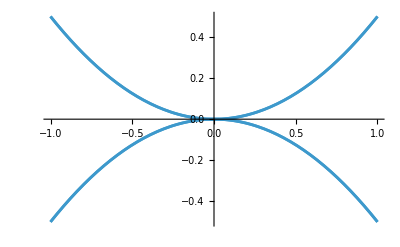

```mathematica
Plot[EigS[{kx,0,0},{0,0,0},1],{kx,-1,1}]
```

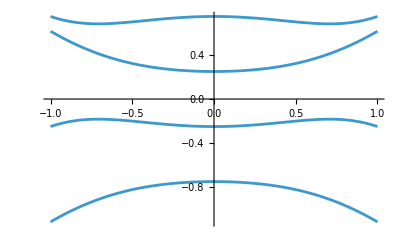

```mathematica
Plot[EigS[{kx,0,0},{0,0,1},1],{kx,-1,1}]
```

```mathematica
SemiMetal=Plot3D[{0,EigS[{0,ky,kz},{0,0,0},1]},{ky,-1,1},{kz,-1,1},BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[255/255,194/255,10/255],Opacity[0.25]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]}},Mesh->None,TicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],AxesStyle->Directive[Black,Thickness[0.005]],
AxesStyle->Directive[Black,Thickness[0.005]],AxesLabel->{Style["k_y",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["k_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["E",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black]},PlotLabel->Style["B⃗ = 0",FontSlant->Italic,FontFamily->"Latin Modern Roman",FontSize->30,FontColor->Black],ViewPoint->{1.2, -2.4, 1.2},ImageSize->500,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}]
Export["SemiMetal.pdf",SemiMetal]
```

-Graphics3D-

SemiMetal.pdf

```mathematica
BMetal=Plot3D[{0,EigS[{0,ky,kz},1/(√2){0,1,0},1]},{ky,-1,1},{kz,-1,1},BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[255/255,194/255,10/255],Opacity[0.25]},{RGBColor[12/255,123/255,220/255],Opacity[0.75]}},Mesh->None,TicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],AxesStyle->Directive[Black,Thickness[0.005]],
AxesStyle->Directive[Black,Thickness[0.005]],AxesLabel->{Style["k_y",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["k_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["E",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black]},PlotLabel->Style["B⃗ = ẑ",FontSlant->Italic,FontFamily->"Latin Modern Roman",FontSize->30,FontColor->Black],ViewPoint->{1.2, -2.4, 1.2},ImageSize->500,Lighting->{"Ambient",White,{1.2, -2.4, 1.2}}]
Export["BMetal.pdf",BMetal]
```

-Graphics3D-

BMetal.pdf

## Landau levels

```mathematica
DeclareNonCommutative[a,a†,q,qs,p]
```

```mathematica
Commutator[a,a†]=1
```

1

Set::write: Tag Commutator in Commutator[a, ConjugateTranspose[a]] is Protected.

```mathematica
p=(a-a†)/(√2 I)
```

-(ⅈ (a-ConjugateTranspose[a]))/(√2)

```mathematica
q=(a+a†)/(√2)
```

(a+ConjugateTranspose[a])/(√2)

```mathematica
ClearAll[B]
```

```mathematica
iqs=I e B q
```

(ⅈ B e (a+ConjugateTranspose[a]))/(√2)

```mathematica
Calc[Commutator[q,p]]
```

-(-(ⅈ (a-ConjugateTranspose[a]))/(√2))**(a+ConjugateTranspose[a])/(√2)+(a+ConjugateTranspose[a])/(√2)**(-(ⅈ (a-ConjugateTranspose[a]))/(√2))

```mathematica
Collect2[DotSimplify[Calc[DotSimplify[DotExpand[-(L[i,1,1](I p).(I p)+L[i,1,2](I p).iqs+L[i,1,3](I p) (I kz)+L[i,1,2]iqs.(I p)+L[i,2,2]iqs.iqs+L[i,2,3]iqs (I kz)+L[i,1,3](I kz)(I p)+L[i,2,3](I kz)iqs+L[i,3,3](I kz)(I kz))]]]],{a,ConjugateTranspose[a],ConjugateTranspose[a].a,ConjugateTranspose[a].ConjugateTranspose[a],a.a,1}]
```

-1/2 ConjugateTranspose[a].ConjugateTranspose[a] (L[i,1,1]-2 ⅈ B e L[i,1,2]-B^2 e^2 L[i,2,2])-1/2 a.a (L[i,1,1]+2 ⅈ B e L[i,1,2]-B^2 e^2 L[i,2,2])+1/2 a.ConjugateTranspose[a] (L[i,1,1]+B^2 e^2 L[i,2,2])+1/2 ConjugateTranspose[a].a (L[i,1,1]+B^2 e^2 L[i,2,2])+√2 a kz (-ⅈ L[i,1,3]+B e L[i,2,3])+√2 kz ConjugateTranspose[a] (ⅈ L[i,1,3]+B e L[i,2,3])+kz^2 L[i,3,3]

```mathematica
Collect2[DotSimplify[Calc[DotSimplify[DotExpand[-(L[i,1,1](I p).(I p)+L[i,1,2](I p).iqs+L[i,1,3](I p) (I kz)+L[i,1,2]iqs.(I p)+L[i,2,2]iqs.iqs+L[i,2,3]iqs (I kz)+L[i,1,3](I kz)(I p)+L[i,2,3](I kz)iqs+L[i,3,3](I kz)(I kz))]]]],{a,ConjugateTranspose[a],ConjugateTranspose[a].a,ConjugateTranspose[a].ConjugateTranspose[a],a.a,1}]//TraditionalForm
```

-1/2 ConjugateTranspose[a].ConjugateTranspose[a] (-B^2 e^2 L(i,2,2)-2 ⅈ B e L(i,1,2)+L(i,1,1))+1/2 a.ConjugateTranspose[a] (B^2 e^2 L(i,2,2)+L(i,1,1))+1/2 ConjugateTranspose[a].a (B^2 e^2 L(i,2,2)+L(i,1,1))-1/2 a.a (-B^2 e^2 L(i,2,2)+2 ⅈ B e L(i,1,2)+L(i,1,1))+√2 kz ConjugateTranspose[a] (B e L(i,2,3)+ⅈ L(i,1,3))+√2 a kz (B e L(i,2,3)-ⅈ L(i,1,3))+kz^2 L(i,3,3)

```mathematica
LandauHam[m_,n_,e_,B_,kz_]:=Module[{a,b,bstar,c,cstar,d,i},a= Sum[(Λ[[i,1,1]]+B^2 e^2 Λ[[i,2,2]])Γ[[i]],{i,1,5}];b=Sum[(1/2  (-Λ[[i,1,1]]+2 ⅈ B e Λ[[i,1,2]]+B^2 e^2 Λ[[i,2,2]]))Γ[[i]],{i,1,5}];bstar=Sum[(1/2 (-Λ[[i,1,1]]-2 ⅈ B e Λ[[i,1,2]]+B^2 e^2 Λ[[i,2,2]]))Γ[[i]],{i,1,5}];
c=Sum[I(-√2  kz (Λ[[i,1,3]]+ⅈ B e Λ[[i,2,3]]))Γ[[i]],{i,1,5}];
cstar=Sum[I(√2 kz  (Λ[[i,1,3]]-ⅈ B e Λ[[i,2,3]]))Γ[[i]],{i,1,5}];
d=Sum[(1/2 (Λ[[i,1,1]]+B^2 e^2 Λ[[i,2,2]]+2 kz^2 Λ[[i,3,3]]))Γ[[i]],{i,1,5}];
KroneckerDelta[m,n](a n+d)+b KroneckerDelta[m,n+2] √(n+2)√(n+1)+bstar KroneckerDelta[m,n-2] √n √(n-1)+c KroneckerDelta[m,n-1] √n+cstar KroneckerDelta[m,n+1] √(n+1)
]
```

```mathematica
ClearAll[LandMat]
```

```mathematica
LandauHam[Quotient[1,3]+1,Quotient[2,3]+1,e,B,kz][[1,1]]
```

-1/6-(B^2 e^2)/6+1/2 (-1/6-(B^2 e^2)/6+(2 kz^2)/3)

```mathematica
Quotient[4,4]
```

1

```mathematica
QuotientRemainder[1,3]
```

{0,1}

```mathematica
RG
```

RG

```mathematica
LandMat[L_,e_,B_,kz_]:=Table[LandauHam[Quotient[m,4]+1,Quotient[n,4]+1,e,B,kz][[QuotientRemainder[m,4][[2]]+1,QuotientRemainder[n,4][[2]]+1]],{m,0,4L},{n,0,4L}]
```

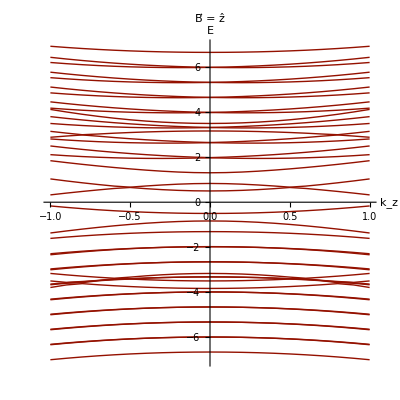

BLL.pdf

```mathematica
LMX=DiscretePlot[Sort[Re[Eigenvalues[LandMat[10,1,1,kz]]]],{kz,-1,1,0.1},AspectRatio->1,Joined->True,Filling->None,PlotStyle->Directive[RGBColor[148/255,17/255,0],Thick],TicksStyle-> Directive[FontSize-> 20,FontFamily -> "Latin Modern Roman",FontColor->Black],AxesStyle->Directive[Black,Thickness[0.005]],
AxesStyle->Directive[Black,Thickness[0.005]],AxesLabel->{Style["k_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black],Style["E",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->25,FontColor->Black]},PlotLabel->Style["B⃗ = ẑ",FontSlant->Italic,FontFamily->"Latin Modern Roman",FontSize->30,FontColor->Black]]
Export["BLL.pdf",LMX]
```